```mathematica
Clear["Global`*"]
```

3 - 9 Steepest descent
Do steepest descent steps when:

3.  f[x] = 2 x_1^2+x_2^2-4 x_1+4 x_2 , x_0=0, 3 steps

I replace the subscripted forms in the problem expression with x and y, which is easier for me to see. I need to mention the Wolfram demonstration by Michael Waters, https://demonstrations.wolfram.com/CurvesOfSteepestDescentFor3DFunctions/, which is appealing and gives the right answer. It is also accommodating about accepting an alien function into its central module.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]=2 x^2+y^2-4 x+4 y
```

-4 x+2 x^2+4 y+y^2

A plot may be useful in reconnoitering the district.

```mathematica
Plot3D[f[x,y],{x,0,15},{y,0,15},AxesLabel->Automatic,ImageSize->150,AspectRatio->Full,ViewPoint->{-4000, 2000, 1000}]
```

-Graphics3D-

First objective is to establish the answer.

```mathematica
FindMinimum[f[x,y],{x,y}]
```

{-6.,{x→1.,y→-2.}}

I see below that step 3 by Mathematica is very close to step 3 by the text answer procedure, whatever that may entail. The text answer for step 3 is {1.037, -1.926}.

```mathematica
pts = Reap[FindMinimum[f[x,y],{{x,-1.2},{y,1}},StepMonitor:>Sow[{x,y}]]][[2,1]]
pts =Join[{{-1.2,1}},pts];
```

{{-0.554696,0.56002},{1.12183,-1.64264},{1.04891,-1.92555},{1.00106,-2.00055},{1.00003,-2.00003},{1.,-2.},{1.,-2.}}

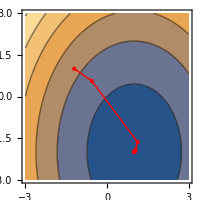

```mathematica
ContourPlot[f[x,y],{x,-3,3},{y,-3,3},Epilog->{Red,Line[pts],Point[pts]},ImageSize->200]
```

9.  f[x]=0.1 x_1^2+x_2^2-0.02 x_1 , x_0=(3, 3), 5 steps

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]=0.1 x^2+y^2-0.02 x
```

-0.02 x+0.1 x^2+y^2

```mathematica
Plot3D[f[x,y],{x,0,15},{y,0,15},AxesLabel->Automatic,ImageSize->150,AspectRatio->Full,ViewPoint->{-4000, 0, 1000}]
```

-Graphics3D-

```mathematica
FindMinimum[f[x,y],{{x,3},{y,3}}]
```

{-0.001,{x→0.1,y→5.96629×10^-11}}

The plot below makes me wonder if it is better not to give a guess about the preferred starting position. The text is interested in step 5, which in its search produced the coordinate {0.11247, -0.00012}.

```mathematica
pts = Reap[FindMinimum[f[x,y],{{x,3},{y,3}},StepMonitor:>Sow[{x,y}]]][[2,1]]
pts =Join[{{-1.2,1}},pts];
```

{{2.79589,0.888522},{2.44241,-0.0226433},{2.16341,-0.0800494},{0.368991,-0.13073},{0.111153,-0.0394899},{0.0942656,-0.0016205},{0.0995506,-0.0000200394},{0.0999956,1.46532×10^-6},{0.1,2.66175×10^-8},{0.1,5.96629×10^-11}}

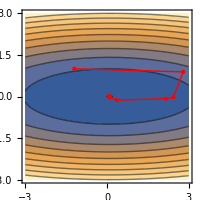

```mathematica
ContourPlot[f[x,y],{x,-3,3},{y,-3,3},Epilog->{Red,Line[pts],Point[pts]},ImageSize->200]
```